```mathematica
<<ProbabilisticBricks`
```

```mathematica
nelx=20;nely=40;
```

```mathematica
generateContacts[]
```

```mathematica
p=Table[{0,0,0,0,0,0},{nelx}];
p[[nelx/4]]={0,0,10,7,0,0};
p[[nelx/4+1]]={0,0,10,7,0,0};
p[[nelx/4-1]]={0,0,10,7,0,0};
p=Flatten[p];
```

```mathematica
setBoundaryConditions[p]
```

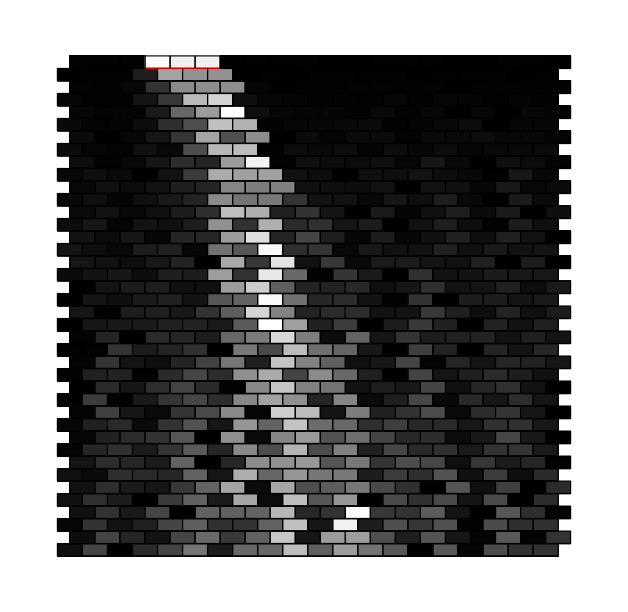

```mathematica
solveProblem[]
```